SciDraw examples: Level schemes

M. A. Caprio, Department of Physics, University of Notre Dame
rev. July 28, 2013

## Package initialization

If you have not already loaded the SciDraw package since starting this Mathematica session, you must do so now.  See the user guide for information first on installing the package and then on loading it at the beginning of each Mathematica session.

```mathematica
Get["SciDraw`"];
```

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.0 (November 24, 2013)
View color paletteVisit home page  -Graphics-

## Examples from the guide

### Levels

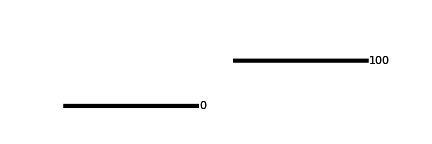

```mathematica
Figure[
FigurePanel[
{
SetOptions[Lev,LineThickness->3];
Lev⟦"lev0"⟧[0,1,0,RightLabel->0];
Lev⟦"lev100"⟧[1,2,100,RightLabel->100];
},
PlotRange->{{0,2},{-50,200}},ExtendRange->Automatic,Frame->False
],
CanvasSize->{6,2}
]
```

### Showing the margins

```mathematica
Figure[
FigurePanel[
{
SetOptions[Lev,LineThickness->3];
Lev⟦"lev0"⟧[0,1,0];
Lev⟦"lev100"⟧[1,2,100];

SetOptions[FigLine,LineDashing->4],
FigLine[{{0,0},{0,100}}];
FigLine[{{1,0},{1,100}}];
FigLine[{{2,0},{2,100}}];

SetOptions[FigLabel,TextOffset->{0,+1},TextNudge->-4];
FigLabel[{0,0},"0"];
FigLabel[{1,0},"1"];
FigLabel[{2,0},"2"];

SetOptions[FigBracket,Color->Red,EndLip->3,EndLength->0,BracketLabel->"Margin",TextOrientation->Vertical,TextOffset->Left,FontSize->14];
FigBracket[Top,10,{0.0,0.1}];
FigBracket[Top,10,{0.9,1.0}];
FigBracket[Top,110,{1.0,1.1}];
FigBracket[Top,110,{1.9,2.0}];

},
PlotRange->{{0,2},{-50,200}},ExtendRange->Automatic,Frame->True
],
CanvasSize->{6,2}
]
```

-Graphics-

### Auto labels (as strings) and gull wings

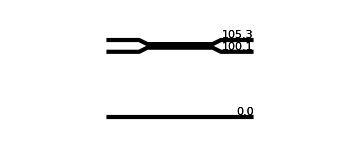

```mathematica
Figure[
FigurePanel[
{
SetOptions[Lev,LineThickness->3];
SetOptions[Lev,RightLabel->Automatic,RightTextOffset->BottomRight];
Lev⟦"lev0"⟧[0,1,"0.0"];
Lev⟦"lev100"⟧[0,1,"100.1",WingHeight->-5];
Lev⟦"lev105"⟧[0,1,"105.3",WingHeight->+5];
},
PlotRange->{{-0.3,1.3},{-20,150}},Frame->False
],
CanvasSize->{5,2}
]
```

### ...or using DecimalDigits on the label

```mathematica
Figure[
FigurePanel[
{
SetOptions[Lev,LineThickness->3];
SetOptions[Lev,RightLabel->Automatic,DecimalDigits->1,RightTextOffset->BottomRight];
Lev⟦"lev0"⟧[0,1,0];
Lev⟦"lev100"⟧[0,1,100.1,WingHeight->-5];
Lev⟦"lev105"⟧[0,1,105.3,WingHeight->+5];
},
PlotRange->{{-0.3,1.3},{-20,150}},Frame->False
],
CanvasSize->{5,2}
]
```

-Graphics-

### Extension line

```mathematica
Figure[
FigurePanel[
{
SetOptions[Lev,LineThickness->3,RightLabel->Automatic,RightTextOffset->BottomRight,FontSize->15];
SetOptions[ExtensionLine,LineDashing->4];
Lev⟦"lev0"⟧[0,1,"0.0"];
ExtensionLine["lev0",Right,0.5];
},
PlotRange->{{-0.3,1.5},{-20,150}},Frame->False
],
CanvasSize->{5,0.4}
]
```

-Graphics-

### Connector

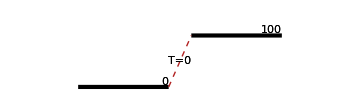

```mathematica
Figure[
FigurePanel[
{
SetOptions[Lev,LineThickness->3,RightLabel->Automatic,RightTextOffset->BottomRight];
Lev⟦"lev0"⟧[0,1,"0"];
Lev⟦"lev100"⟧[1,2,"100"];
SetOptions[Connector,LineDashing->4,LineColor->Firebrick,TextBackground->Automatic];
Connector["lev0","lev100",CenterLabel->Row[{textit["T"],"=0"}]];

},
PlotRange->{{-0.3,2.3},{-20,150}},Frame->False
],
CanvasSize->{5,1.5}
]
```

### Band labels and Do loops

```mathematica
Figure[
FigurePanel[
{
SetOptions[Lev,LineThickness->2];

(* bands *)
Do[
Lev⟦{"lev",J,1}⟧[0,1,J*(J+1)/6*100,LeftLabel->LevelLabel[{J,1,+1}]],
{J,0,6,2}
];
BandLabel[{"lev",0,1},Row[{textit["K"],"=0"}]];

WithOrigin[
1.5,
{
Lev⟦{"lev",2,2}⟧[0,1,1000,LeftLabel->LevelLabel[{2,2,+1}]]
}
];
BandLabel[{"lev",2,2},Row[{textit["K"],"=2"}]]; 

(* transitions *)
Do[
Trans[{"lev",J,1},{"lev",J-2,1}],
{J,2,6,2}
];
Trans[{"lev",2,2},{"lev",2,1},EndPositions->{0.25,0.9}];

(* panel label *)
FigLabel[Scaled[{0.8,0.3}],Isotope[100,"X"],FontSize->16]

},
PlotRange->{{0,2},{0,1000}},ExtendRange->0.2,Frame->False
],
CanvasSize->{3,3}
]
```

-Graphics-

### Basic example of Trans

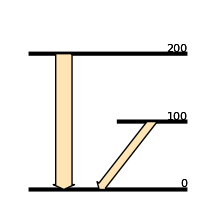

```mathematica
Figure[
FigurePanel[
{

(* appearance settings *)
SetOptions[Lev,LineThickness->3];
SetOptions[Trans,ArrowType->"Block",FillColor->Moccasin];

(* turn on energy labels *)
SetOptions[Lev,RightLabel->Automatic,TextOffset->BottomRight];

(* levels *)
Lev⟦"lev0"⟧[0,2,0];
Lev⟦"lev100"⟧[1,2,100];
Lev⟦"lev200"⟧[0,2,200];

(* transitions *)
Trans["lev200",0.5,"lev0",Automatic,Width->20]; (* note use of Automatic *)
Trans["lev100",0.5,"lev0",0.9,Width->10];


},
PlotRange->{{0,2},{-10,250}},Frame->False
], 
CanvasSize->{3,3}
]
```

### Transition with intermediate points

```mathematica
Figure[
FigurePanel[
{
SetOptions[Lev,LineThickness->2];
SetOptions[Trans,Color->Firebrick,FontSize->14];
Lev⟦"leva"⟧[0,1,0];
Lev⟦"levb"⟧[1,2,0];

Trans[
"leva","levb",
IntermediatePoints->{FromTail[Canvas[{20,20}]],FromHead[Canvas[{-20,20}]]},
RightLabel->100
];

},
PlotRange->{{0,2},{-1,1}},Frame->False],
CanvasSize->{2,1}
]
```

-Graphics-

### More transitions with intermediate points (for beta decay scheme)

```mathematica
Figure[
FigurePanel[
{
SetOptions[FigObject,FontSize->14];
SetOptions[Lev,LineThickness->3,RightLabel->Automatic,LeftTextOffset->BottomLeft,RightTextOffset->BottomRight,RightTextNudge->+0.5];
SetOptions[Lev,Margin->0.2];
SetOptions[Trans,
EndPositions->{0.2,0.8},IntermediatePoints->{FromTail[{-0.10,0}],FromHead[{+0.30,0}]},
HeadLength->5,HeadLip->2,
Color->Firebrick,TextBackground->Automatic,TextOrientation->Horizontal,
CenterTextOffset->Right, (* for right alignment of labels *)
CenterLabelPosition->{-1,0.2} (* for label at fraction 0.2 into last segment -- see below *)
];

(* daughter levels *)
WithOrigin[
{0,0},
{
Lev⟦{"daughter",0}⟧[0,1,0,LeftLabel->LevelLabel[{1,None,+1}]];
Lev⟦{"daughter",40}⟧[0,1,40,LeftLabel->LevelLabel[{1,None,+1}]];
}
];

(* parent levels *)
WithOrigin[
{1,90},
{
Lev⟦{"parent",0}⟧[0,1,0,LeftLabel->LevelLabel[{0,None,+1}]];
}
];

Trans[{"parent",0},{"daughter",0},CenterLabel->100];
Trans[{"parent",0},{"daughter",40},CenterLabel->80];

},
PlotRange->{{0,2},{-10,100}},Frame->False
],
CanvasSize->{4,2}
]
```

-Graphics-

### Gallery of arrow types (with geometry parameters indicated)

```mathematica
MarkerBracketHorizontal[yc_,{xc1_,xc2_},l_String,Opts___?OptionQ]:=FigBracket[
Top,
RelativeTo[{0,0},Canvas[{0,yc}]],
{RelativeTo[{0,0},Canvas[{xc1,0}]],RelativeTo[{0,0},Canvas[{xc2,0}]]},
Opts,
BracketLabel->l,
TextOrientation->Vertical,TextOffset->Left
];
MarkerBracketVertical[xc_,{yc1_,yc2_},l_String,Opts___?OptionQ]:=FigBracket[
Right,
RelativeTo[{0,0},Canvas[{xc,0}]],
{RelativeTo[{0,0},Canvas[{0,yc1}]],RelativeTo[{0,0},Canvas[{0,yc2}]]},
Opts,
HeadLabel->l,
TextOrientation->Vertical,TextOffset->Left
];
Figure[
FigurePanel[
{
SetOptions[Lev,Show->False];
Lev⟦"lev0"⟧[0,1,0];
Lev⟦"lev100"⟧[0,1,100];

SetOptions[Trans,LineThickness->2,LineColor->Black,FillColor->Moccasin,HeadLength->20];
Trans["lev100",0.0,"lev0",Automatic,ArrowType->"Line",HeadLip->15];
Trans["lev100",1.0,"lev0",Automatic,ArrowType->"DoubleLine",HeadLip->12,Width->30];
Trans["lev100",2.0,"lev0",Automatic,ArrowType->"Block",HeadLip->15,Width->30];
Trans["lev100",3.2,"lev0",Automatic,ArrowType->"Squiggle",HeadLip->20,Width->30,SquiggleWavelength->25,PlotPoints->128];

SetOptions[FigLabel,TextOffset->{0,+1},TextNudge->-4];
FigLabel[{0,0},"\"Line\""];
FigLabel[{1,0},"\"DoubleLine\""];
FigLabel[{2,0},"\"Block\""];
FigLabel[{3.2,0},"\"Squiggle\""];

SetOptions[FigBracket,Color->Firebrick,EndLength->0,EndLip->3,FontSize->12],


WithOrigin[
0,
{
MarkerBracketHorizontal[20+15,{0,15},"HeadLip",TextNudge->{2,0}];
MarkerBracketVertical[15+8,{0,20},"HeadLength",TextNudge->{2,0}];
};
];

WithOrigin[
1,
{
MarkerBracketHorizontal[20+30,{-15,15},"Width"];
MarkerBracketHorizontal[20+15,{15,15+12},"HeadLip",TextNudge->{2,0}];
MarkerBracketVertical[15+12 +5,{0,20},"HeadLength",TextNudge->{2,0}];
};
];

WithOrigin[
2,
{
MarkerBracketHorizontal[20+30,{-15,15},"Width"];
MarkerBracketHorizontal[20+15,{15,15+12},"HeadLip",TextNudge->{2,0}];
MarkerBracketVertical[15+12 +5,{0,20},"HeadLength",TextNudge->{2,0}];
};
];

WithOrigin[
3.2,
{
MarkerBracketHorizontal[20+30,{-15,15},"Width",TextBackground->Automatic];
MarkerBracketHorizontal[20+15,{-20,0},"HeadLip",TextNudge->{2,0},BracketLabelPosition->0,BracketTextOffset->Bottom];
MarkerBracketVertical[15+12 +5,{0,20},"HeadLength",TextNudge->{2,0}];
};
];

},
PlotRange->{{-0.5,4.0},{-20,110}},Frame->False
],
CanvasSize->{5,2.3}
]
```

-Graphics-

### Some arrow varieties

```mathematica
Figure[
FigurePanel[
{
SetOptions[Lev,Margin->-0.2,LineThickness->3];
Lev⟦"lev0"⟧[0,3.5,0];
Lev⟦"lev100"⟧[0,3.5,100];

SetOptions[Trans,LineThickness->2,FillColor->Moccasin,TextOrientation->Horizontal,TextColor->Firebrick,FontSize->12,TextOffset->Top,TextNudge->-4,TextPadding->True (* for alignment *)];

Trans[
"lev100","lev0",EndPositions->0.2+{0.5,0},
ArrowType->"Line",IntermediatePoints->{FromHead[{0.3,25}]},
HeadLabel->"Bent arrow"
];

Trans[
"lev100","lev0",EndPositions->0.5+{0.5,0},Width->10,
ArrowType->"DoubleLine",IntermediatePoints->{FromHead[{0.3,25}]}
(*HeadLabel->"Bent arrow"*)
];


Trans[
"lev100","lev0",EndPositions->1.3+{0.5,0},
ArrowType->"DoubleLine",ShowTail->True,Width->5,
HeadLabel->StackText[Center,0,{"Double-headed","arrow"}]
];

Trans[
"lev100","lev0",EndPositions->2.2+{0.5,0},
ArrowType->"Block",Width->20,
HeadLabel->"Flush…"
];

Trans["lev100","lev0",EndPositions->2.7+{0.5,0},
ArrowType->"Block",Width->20,TailFlush->False,
HeadLabel->"or not"
];

},
PlotRange->{{-0.5,4.5},{-50,120}},Frame->False
],
CanvasSize->{6,2.5}
]
```

-Graphics-

### Arrow label sides

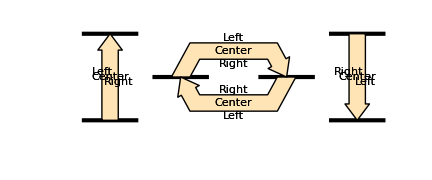

```mathematica
Figure[
FigurePanel[
{

SetOptions[Lev,LineThickness->3];
SetOptions[Trans,FillColor->Moccasin,TextColor->Firebrick,FontSize->14,ArrowType->"Block",Width->20,HeadLength->20,HeadLip->5];

WithOrigin[
0,
{
Lev⟦"lev0"⟧[0,1,0];
Lev⟦"lev100"⟧[0,1,100];
Trans[
"lev0","lev100",EndPositions->{0.5,0.5},
LeftLabel->"Left",
RightLabel->"Right",
CenterLabel->"Center"
];
}
];

WithOrigin[
1,
{
Lev⟦"lev50a"⟧[0,1,50];
Lev⟦"lev50b"⟧[1.5,2.5,50];
Trans[
"lev50a","lev50b",EndPositions->{0.5,0.5},
IntermediatePoints->{FromTail[{0.2,30}],FromHead[{-0.2,30}]},
LeftLabel->"Left",
RightLabel->"Right",
CenterLabel->"Center"
];
Trans[
"lev50b","lev50a",EndPositions->{0.5,0.5},
IntermediatePoints->{FromTail[{-0.2,-30}],FromHead[{0.2,-30}]},
LeftLabel->"Left",
RightLabel->"Right",
CenterLabel->"Center"
];
}
];

WithOrigin[
3.5,
{
Lev⟦"lev0"⟧[0,1,0];
Lev⟦"lev100"⟧[0,1,100];
Trans[
"lev100","lev0",EndPositions->{0.5,0.5},
LeftLabel->"Left",
RightLabel->"Right",
CenterLabel->"Center"
];
}
];


},
PlotRange->{{-0.5,4.5},{-50,120}},Frame->False
],
CanvasSize->{6,2.5}
]
```

### Arrow segments

Note we use FigLabel and FigAnchor to make the labels

```mathematica
Figure[
FigurePanel[
{

SetOptions[Lev,Show->False,Margin->0];
SetOptions[FigLabel,FillColor->Moccasin,TextColor->Firebrick];



Lev⟦"leva"⟧[-2,0,0];  (* center at -1 *)
Lev⟦"levb"⟧[0,2,0]; (* center at +1 *)
Trans⟦"trans"⟧[
"leva","levb",EndPositions->{1,1},
IntermediatePoints->{{-1/2,Sqrt[3]/2},{1/2,Sqrt[3]/2}}
];
Do[
FigLabel[
FigAnchor["trans",Left,{i,0.5}],
i,FontSize->15
],
{i,1,3}
];
Do[
FigLabel[
FigAnchor["trans",Right,{i,0.5}],
i,FontSize->12
],
{i,-1,-3,-1}
];

},
PlotRange->{{-1,+1},{0,2}},Frame->False
],
CanvasSize->{4,2}
]
```

-Graphics-

### Arrow label orientations

```mathematica
Figure[
FigurePanel[
{

SetOptions[Lev,Show->False];
SetOptions[Trans,FillColor->Moccasin,TextColor->Firebrick,FontSize->14];

WithOrigin[
0,
{
Lev⟦"lev0"⟧[0,1,0];
Lev⟦"lev100"⟧[0,1,100];
Trans[
"lev100","lev0",EndPositions->{0.5,0.3},
RightLabel->"Automatic"
];
Trans[
"lev100","lev0",EndPositions->{0.5,0.7},
LeftLabel->"Automatic"
];
}
];

WithOrigin[
1,
{
Lev⟦"lev0"⟧[0,1,0];
Lev⟦"lev100"⟧[0,1,100];
Trans[
"lev100","lev0",EndPositions->{0.5,0.3},
RightLabel->"Inverse",RightTextOrientation->Inverse
];
Trans[
"lev100","lev0",EndPositions->{0.5,0.7},
LeftLabel->"Automatic"
];
}
];

SetOptions[Trans,FillColor->Moccasin,TextColor->Firebrick,FontSize->14,ArrowType->"Block",Width->20,HeadLength->20,HeadLip->5];
WithOrigin[
2,
{
Lev⟦"lev0"⟧[0,1,0];
Lev⟦"lev100"⟧[0,1,100];
Trans[
"lev100","lev0",EndPositions->{0.7,0.3},
CenterLabel->"Automatic",CenterLabelPosition->0.4,
TailLabel->"Vertical",TailTextOrientation->Vertical,TailTextOffset->Left,  (* that's the left end of the text *before* rotation! *)
LeftLabel->"Horizontal",LeftTextOrientation->Horizontal,LeftTextOffset->TopLeft
];

}
];


},
PlotRange->{{-0.5,4.5},{-50,200}},Frame->False
],
CanvasSize->{6,3}
]
```

-Graphics-

### Transition autospacing for decay schemes

```mathematica
Figure[
FigurePanel[
{

SetOptions[FigObject,FontSize->12];
SetOptions[Lev,LineThickness->2,RightLabel->Automatic,RightTextOffset->BottomRight,LeftTextOffset->BottomLeft,WingTipWidth->25,Margin->0];

(* levels *)
Lev⟦"lev0"⟧[0,1,"0",LeftLabel->LabelJP[0,+1]];
Lev⟦"lev121"⟧[0,1,"121",LeftLabel->LabelJP[2,+1]];
Lev⟦"lev366"⟧[0,1,"366",LeftLabel->LabelJP[4,+1]];
Lev⟦"lev684"⟧[0,1,"684",LeftLabel->LabelJP[0,+1],WingHeight->-5];
Lev⟦"lev706"⟧[0,1,"706",LeftLabel->LabelJP[6,+1],WingHeight->+5];
Lev⟦"lev810"⟧[0,1,"810",LeftLabel->LabelJP[2,+1]];
Lev⟦"lev963"⟧[0,1,"963",LeftLabel->LabelJP[1,-1]];

(* autospaced transitions *)
SetOptions[Trans,TextBackground->Automatic,TextMargin->1,TextNudge->2];
AutoLevelInit[0.85,-0.04,-0.08];
AutoLevel["lev121"];
AutoTrans["lev0",TailLabel->"121"];
AutoLevel["lev366"];
AutoTrans["lev121",TailLabel->"244"];
AutoLevel["lev684"];
AutoTrans["lev121",TailLabel->"562"];
AutoTrans["lev0",TailLabel->"684",LineColor->Firebrick,LineDashing->4];
AutoLevel["lev706"];
AutoTrans["lev366",TailLabel->"340"];
AutoLevel["lev810"];
AutoTrans["lev684",TailLabel->"125",LineColor->Firebrick];
AutoTrans["lev366",TailLabel->"443"];
AutoTrans["lev121",TailLabel->"688"];
AutoTrans["lev0",TailLabel->"810"];
AutoLevel["lev963"];
AutoTrans["lev810",TailLabel->"152",LineColor->Ultramarine];
AutoTrans["lev684",TailLabel->"278",LineColor->Ultramarine];
AutoTrans["lev121",TailLabel->"841",LineColor->Ultramarine];
AutoTrans["lev0",TailLabel->"963",LineColor->Ultramarine];

},
PlotRange->{{-0.1,1.1},{-20,1200}},Frame->False
],
CanvasSize->{6,3}
]
```

-Graphics-

## More sophisticated examples

### Two-panel level scheme

Adapted from M. A. Caprio, Ph.D. thesis, Yale University (2003), arXiv:nucl-ex/0502004.

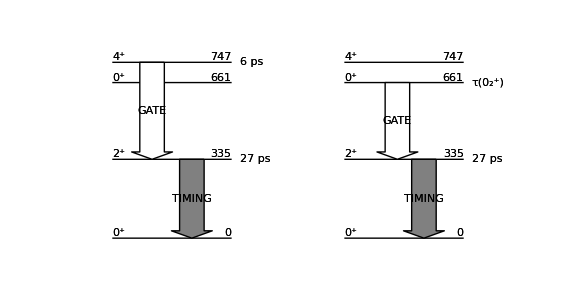

```mathematica
Figure[
FigurePanel[{

(* set default styles for level scheme objects *)

SetOptions[FigObject,FontSize->20];
SetOptions[Lev,RightLabel->Automatic,LeftTextOffset->BottomLeft,RightTextOffset->BottomRight];
SetOptions[Trans,ArrowType->"Block",HeadLength->9,HeadLip->10,Width->30,
CenterTextOrientation->Horizontal,CenterTextBackground->Automatic
];

DefineStyle["timing",{Trans->{FillColor->Gray,CenterLabel->"TIMING",CenterTextColor->Firebrick}}];
DefineStyle["gate",{Trans->{FillColor->White,CenterLabel->"GATE",CenterTextColor->DarkGreen}}];
DefineStyle["lifetime",{FigLabel->{Displacement->Canvas[{10,0}],TextColor->Firebrick}}];

(* draw cascade from 4+ level *)

WithOrigin[
0,
{
(*FigLabel[{-.4,850},"(a)",TextOffset->{-1,1}];*)

Lev⟦"lev0a"⟧[0,2,"0",LeftLabel->LabelJP[0]];
Lev⟦"lev335a"⟧[0,2,"335",LeftLabel->LabelJP[2]];
FigLabel["lev335a",Right,"27 ps",Style->"lifetime"];
Lev⟦"lev661a"⟧[0,2,"661",LeftLabel->LabelJP[0]];
Lev⟦"lev747a"⟧[0,2,"747",LeftLabel->LabelJP[4]];
FigLabel["lev747a",Right,"  6 ps",Style->"lifetime"];
Trans["lev335a",1.3,"lev0a",Automatic,Style->"timing"];
Trans["lev747a",.7,"lev335a",Automatic,Style->"gate"];
}
];

(* draw cascade from 0+ level *)

WithOrigin[
3.5,
{
(*FigLabel[{-.4,850},"(b)",TextOffset->{-1,1}];*)

Lev⟦"lev0b"⟧[0,2,"0",LeftLabel->LabelJP[0]];
Lev⟦"lev335b"⟧[0,2,"335",LeftLabel->LabelJP[2]];
FigLabel["lev335b",Right,"27 ps",Style->"lifetime"];
Lev⟦"lev661b"⟧[0,2,"661",LeftLabel->LabelJP[0]];
FigLabel["lev661b",Right,Row[{"τ(",hspace[-0.2],LabelJiP[0,2],")"}],Style->"lifetime"];
Lev⟦"lev747b"⟧[0,2,"747",LeftLabel->LabelJP[4]];
Trans["lev335b",1.3,"lev0b",Automatic,Style->"timing"];
Trans["lev661b",.9,"lev335b",Automatic,Style->"gate"];
}
];


},
PlotRange->{{-.8,6.3},{-100,900}},Frame->False
],
CanvasSize->{8,4}
]
```

### Level scheme combining various styles of transition arrow

Adapted from M. A. Caprio, Ph.D. thesis, Yale University (2003), arXiv:nucl-ex/0502004.

```mathematica
Figure[
FigurePanel[
{
SetOptions[FigObject,FontSize->14];
SetOptions[Lev,LeftTextOffset->BottomLeft,RightTextOffset->BottomRight];
SetOptions[Trans,HeadLength->9, HeadLip->3,ArrowType->Block];

Lev⟦"lev100"⟧[0,1,0,LeftLabel->LabelJP[0]];
Lev⟦"lev112"⟧[0,1,556,LeftLabel->LabelJP[2]];
Lev⟦"lev124"⟧[0,1,1276,LeftLabel->LabelJP[4]];
Lev⟦"lev122"⟧[1,2,1534,LeftLabel->LabelJP[2]];

Lev⟦"lev136"⟧[0,1,2110.9,LeftLabel->LabelJP[6]];
Lev⟦"lev134"⟧[1,2,2138,LeftLabel->LabelJP[4]];
Lev⟦"lev133"⟧[2,3,2111.5,LeftLabel->LabelJP[3]];

WithOrigin[
3.25,
{
Lev⟦"lev01"⟧[0,1,1593,LeftLabel->LabelJP[0],RightLabel->Automatic];
ExtensionLine["lev100",Right,2];
Trans["lev01",.6,"lev100",2.4,Width->20,FillColor->White,CenterLabel->Row[{Superscript["ρ",2],"(",textit["E"],"0)=4.0(15)×",Superscript[10,-3]}],CenterLabelPosition->0.6];
Trans["lev01",.4,"lev112",.5,ArrowType->Line,LineDashing->2,RightLabel->"<0.0004 W.u."];
Trans["lev01",.05,"lev122",.95,TailFlush->False,Width->20,FillColor->Gray,LeftLabel->"96(40) W.u."];
}
];

WithOrigin[
4.5,
{
Lev⟦"lev02"⟧[0,1,1658,LeftLabel->LabelJP[0],RightLabel->Automatic];
Trans["lev02",0.5,"lev112",0.8,Width->3,FillColor->Gray,LeftLabel->"13(3) W.u.",LeftLabelPosition->0.2];
Trans["lev02",0.6,"lev100",2.75,ArrowType->Line,LineDashing->2,LeftLabel->Row[{Superscript["ρ",2],"(",textit["E"],"0)<0.3×",Superscript[10,-3]}],RightTextBuffer->1.5];
}
];

},
PlotRange->{{-0.5,7},{-100,2300}},
Frame->False
],
CanvasSize->{7.5,4.5}
]
```

-Graphics-

### Beta decay scheme

Note: The SciDraw layered drawing system is necessary to prevent the white-out boxes behind the labels from obstructing the neighboring labels.  To see what would happen if there were no layered drawing system, temporarily disable layering by including
	SetOptions[FigObject,Layer→0].
at the beginning of the scheme.

Adapted from E. A. McCutchan et al., Phys. Rev. C 71, 024309 (2005).
Courtesy of E. A. McCutchan.

```mathematica
Figure[
FigurePanel[{

SetOptions[FigObject,FontSize->20,LineThickness->2],
SetOptions[Lev,RightLabel->Automatic,WingSlopeWidth->10,WingTipWidth->60];
SetOptions[Trans,HeadLength->6,HeadLip->3,TextBackground->Automatic,TextMargin->2,TailTextNudge->2];

(* title *)
FigLabel[{7,-100},"^166Hf",FontSize->35];

(* levels *)
Lev⟦"lev0"⟧[0,14,"0.0",LeftLabel->"0^+"];
Lev⟦"lev159"⟧[0,14,"158.6",LeftLabel->"2^+"];
Lev⟦"lev470"⟧[0,14,"470.5",LeftLabel->"4^+"];
Lev⟦"lev810"⟧[0,14,"809.9",WingHeight->-5,LeftLabel->"2^+"];
Lev⟦"lev897"⟧[0,14,"897.2", LeftLabel->"6^+",WingHeight->-3];
Lev⟦"lev1006"⟧[0,14,"1007.1",WingHeight->-7, LeftLabel->"3^+"];
Lev⟦"lev1065"⟧[0,14,"1065.0",WingHeight->+5, LeftLabel->"(0^+)"];
Lev⟦"lev1164"⟧[0,14,"1162.7"];
Lev⟦"lev1219"⟧[0,14,"1218.8",WingHeight->+8, LeftLabel->"(2^+)"];
Lev⟦"lev1332"⟧[0,14,"1332.4"];
Lev⟦"lev1405"⟧[0 ,14,"1404.6"];
Lev⟦"lev1551"⟧[0,14,"1551.4", LeftLabel->"(5^+)",WingHeight ->-7];
Lev⟦"lev1603"⟧[0,14,"1603.2"];

(* transitions *)
AutoLevelInit[12.2,-0.5,-0.5];
AutoLevel["lev159"];
AutoTrans["lev0",TailLabel->"159  100"];

AutoLevel["lev470"];
AutoTrans["lev159",TailLabel->"312  44.7"];

AutoLevel["lev810"];
AutoTrans["lev0",TailLabel->"810  20.2"];
AutoTrans["lev159",TailLabel->"651  18.9"];

AutoLevel["lev897"];
AutoTrans["lev470",TailLabel->"427  1.2"];

AutoLevel["lev1006"];
AutoTrans["lev159",TailLabel->"848  12.7"];
AutoTrans["lev470",TailLabel->"537  2.0"];

AutoLevel["lev1065"];
AutoTrans["lev159",TailLabel->"906  2.1"];

AutoLevel["lev1164"];
AutoTrans["lev470",TailLabel->"692  4.4"];

AutoLevel["lev1219"];
AutoTrans["lev0",TailLabel->"1219  1.0"];
AutoTrans["lev159",TailLabel->"1060  2.3"];
AutoTrans["lev470",TailLabel->"748  3.0"];

AutoLevel["lev1332"];
AutoTrans["lev159",TailLabel->"1174  5.9"];
AutoTrans["lev470",TailLabel->"862  5.4"];

AutoLevel["lev1405"];
AutoTrans["lev159",TailLabel->"1246  5.4"];
AutoTrans["lev810",TailLabel->"595  5.7"];
AutoTrans["lev1006",TailLabel->"398  2.9"];

AutoLevel["lev1551"];
AutoTrans["lev470",TailLabel->"1081  1.6"];
AutoTrans["lev1006",TailLabel->"544  0.9"];

AutoLevel["lev1603"];
AutoTrans["lev159",TailLabel->"1444  2.3"];
AutoTrans["lev470",TailLabel->"1134  2.5" ];


},
PlotRange->{{-1,16},{-200,1910}},Frame->False
],
CanvasSize->{8.5,8}
]
```

-Graphics-

### Nuclear shell model diagram

Example of writing simple functions to automatically create the list of levels to plot, calcule the level energies, generate the labels, etc.

Labeling -- spectroscopic notation and color scheme for levels

Note: The letter ℏ is “HBar”, entered as Escape - h - b - Escape.

(* SciDraw provides the following definitions for spdfg... spectroscopic notation: *)
SpectroscopicLetter[0] = "s";
SpectroscopicLetter[1] = "p";
SpectroscopicLetter[2] = "d";
SpectroscopicLetter[3] = "f";
SpectroscopicLetter[4] = "g";
SpectroscopicLetter[5] = "h";
SpectroscopicLetter[6] = "i";
SpectroscopicLetter[7] = "j";
SpectroscopicLetter[8] = "k";
ShellLabel[{n_,l_,j_}]:=Row[{n,Subscript[SpectroscopicLetter[l],SolidusFractionize[j]]}];

Level set: {{0,0,1/2},{0,1,1/2},{0,1,3/2},{1,0,1/2},{0,2,3/2},{0,2,5/2},{1,1,1/2},{1,1,3/2},{0,3,5/2},{0,3,7/2},{0,4,9/2}}

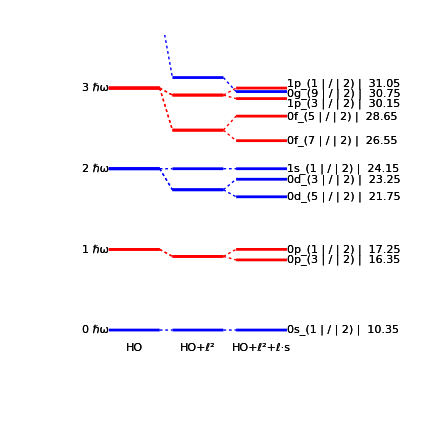

```mathematica
(* define functions for coloring orbitals by parity of major shell *)

ShellGrade[{n_,l_,j_}]:=Mod[2*n+l,2];
ShellColor[{n_,l_,j_}]:=Switch[ShellGrade[{n,l,j}],0,Blue,1,Red];

(* define energy function *)

ESM[{ho_,D_,xi_},{n_,l_,j_}]:=(2*n+l+3/2)*ho+D*l*(l+1)+1/2*xi*(+l*KroneckerDelta[j,l+1/2]-(l+1)*KroneckerDelta[j,l-1/2]);

(* define function to generate set of orbitals by major shell *)

LevelSetOrbital[N_]:=Table[{1/2*(N-l),l},{l,Mod[N,2],N,2}];
LevelSetSpinOrbit[NMax_]:=Module[
{n,l,j},
Last[Last[Reap[
Do[
{n,l}=nl;
j=l+sigma*1/2;
If[j>0,Sow[{n,l,j}]],
{N,0,NMax},{nl,LevelSetOrbital[N]},{sigma,{-1,+1}}
]
]]]
];

(* define level set to plot: levels through N=3 plus g9/2 orbit *)

PlotLevelSet=Append[
LevelSetSpinOrbit[3],
{0,4,9/2}
];
Print["Level set: ",PlotLevelSet];

(* make figure *)

HOParams={6.9,-0.3,-0.6};
HOParams0=HOParams*{1,0,0};
HOParams1=HOParams*{1,1,0};
HOParams2=HOParams*{1,1,1};
Figure[
FigurePanel[
{

SetOptions[Lev,LineThickness->2];
SetOptions[Connector,LineDashing->2];
WithOrigin[
0,
{
Table[
Lev⟦{"lev",nlj,0}⟧[0,1,ESM[HOParams0,nlj],
Color->ShellColor[nlj],
LeftTextOffset->{+1,0},
Switch[
nlj,
{0,l_,j_}/;(j==l+1/2),LeftLabel->Row[{nlj[[2]]," ℏω"}],
_,{}
]
],
{nlj,PlotLevelSet}
];
}
];

WithOrigin[
1,
{
Table[
{
Lev⟦{"lev",nlj,1}⟧[0,1,ESM[HOParams1,nlj],Color->ShellColor[nlj]],
Connector[{"lev",nlj,0},{"lev",nlj,1},Color->ShellColor[nlj]]
},
{nlj,PlotLevelSet}
]
}
];

WithOrigin[
2,
{
SetOptionOverrides[
{
{"lev",{1,1,3/2},2}->{RightTextNudge->-6},
{"lev",{0,4,9/2},2}->{RightTextNudge->-3},
{"lev",{1,1,1/2},2}->{RightTextNudge->+6}
}
];
Table[
{
Lev⟦{"lev",nlj,2}⟧[0,1,ESM[HOParams2,nlj],
Color->ShellColor[nlj],
RightLabel->Grid[{{ShellLabel[nlj],FixedPointForm[ESM[HOParams2,nlj],2]}},ItemSize->3,Spacings->0],
RightTextOffset->{-1,0}
];
Connector[{"lev",nlj,1},{"lev",nlj,2},Color->ShellColor[nlj]]
},
{nlj,PlotLevelSet}
]
}
];

SetOptions[BandLabel,TextOffset->Bottom,TextNudge->-25];  (* align bottoms rather than top of subscript *)
BandLabel[{"lev",{0,0,1/2},0},"HO"];
BandLabel[{"lev",{0,0,1/2},1},Row[{"HO+",Superscript[textbf["ℓ"],2]}]];
BandLabel[{"lev",{0,0,1/2},2},Row[{"HO+",Superscript[textbf["ℓ"],2],"+",textbf["ℓ"],"·",textbf["s"]}]];

},
PlotRange->{{-1,4},{5,35}},Frame->False
],
CanvasSize->{6,6}
]
```

### Molecular potentials and spectra: Combining plots and level schemes in one figure

This figure illustrates several possibilities for drawing a figure:

	1. Creating multipanel plots with unequal panel sizes, gaps between panels, and colored frames
	
	2. Including functions in a plot, and controlling their appearance through FigLine
	
	3. Drawing axes with FigAxis
	
	4. Annotating plots with drawing objects, here FigCircle
	
	5. Defining functions (here U2Lev and SO3Lev) to draw levels based on energy formulas
	
	6. Using Table to construct level schemes with many levels automatically	
	
Note: The letter ℰ is “ScriptCapitalE”, entered as Escape - s - c - E - Escape.

```mathematica
U2Lev[k_,n_]:=Lev⟦{"lev","U2",k,n}⟧[k,k+1,epsilon*n,LeftLabel->n-2*k];
SO3Lev[v_,l_]:=Lev⟦{"lev","SO3",v,l}⟧[v,v+1,v+b*l^2,LeftLabel->l];

Figure[
Multipanel[
{

(* set up drawing options *)
SetOptions[FigObject,FontSize->12];
SetOptions[Lev,LeftTextOffset->{+1,0},LineThickness->2,Margin->0.2,WingTipWidth->10,WingSlopeWidth->5];
SetOptions[FigLine,LineThickness->2];
SetOptions[FigAxis,HeadExtension->0,FontSize->15];
DefineStyle["panellabel",{FigLabel->{Point->Scaled[{0.7,0.2}],FontSize->20}}];

(* set up multipanel plot *)


(* draw functions *)
FigurePanel[
{
FigAxis[Bottom,0,{0,3.2},AxisLabel->textit["r"]];
FigAxis[Left,0,{-0.1,1},AxisLabel->"ℰ"];
FigLine[Plot[(1+r^2)^(-1)*r^2,{r,0,3}]];
FigCircle[{0,0},Radius->Canvas[3],Color->VenetianRed];
},
{1,1},
XPlotRange->{-0.6,3.5},YPlotRange->{-0.4,1.3}
];

FigurePanel[
{
FigAxis[Bottom,0,{0,3.2},AxisLabel->textit["r"]];
FigAxis[Left,0,{-1.1,0.2},AxisLabel->"ℰ"];
FigLine[Plot[-4*(1+r^2)^(-2)*r^2,{r,0,3}]];
FigCircle[{1,-1},Radius->Canvas[3],Color->Blue];
},
{2,1},
XPlotRange->{-0.6,3.5},YPlotRange->{-1.5,0.5}
];

(* draw level schemes *)

FigurePanel[
{
SetOptions[Lev,LineColor->VenetianRed];
epsilon=0.6;
Table[U2Lev[k,n],{k,0,2},{n,2*k,4}];
Table[FigLabel[{"lev","U2",0,n},Left,RowBox[{textit["n"],"=",n}],Displacement->Canvas[{-15,0}]],{n,0,4}];
FigLabel["U(2)",Style->"panellabel"]
},
{1,2},
XPlotRange->{-0.8,3.2},YPlotRange->{-0.5,3}
];

FigurePanel[
{
SetOptions[Lev,LineColor->Blue];
b=0.15;
Table[SO3Lev[0,l],{l,0,4}];
Table[SO3Lev[1,l],{l,0,3}];
Table[SO3Lev[2,l],{l,0,2}];
Table[BandLabel[{"lev","SO3",v,0},RowBox[{textit["v"],"=",v}]],{v,0,2}];
FigLabel["SO(3)",Style->"panellabel"]
},
{2,2},
XPlotRange->{-0.2,3.2},YPlotRange->{-0.5,3}
];

},
Dimensions->{2,2},
(* panel appearance *)
LineColor->Gray,ShowTicks->False,
PanelLetter->None,
(* panel array geometry *)
XPanelSizes->{0.6,1},XPanelGaps->0.1,
YPanelGaps->0.1
],
CanvasSize->{6,7}
]
```

-Graphics-